## Basic tests

### Pauli matrices

```mathematica
sx//MatrixForm
```

(0 | 1
1 | 0)

```mathematica
sy//MatrixForm
```

(0 | -ⅈ
ⅈ | 0)

```mathematica
sz//MatrixForm
```

(1 | 0
0 | -1)

### Symbolic matrix

```mathematica
A=SymbolicMatrix[a,9];
```

```mathematica
A//MatrixForm
```

(a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4) | a_(1,5) | a_(1,6) | a_(1,7) | a_(1,8) | a_(1,9)
a_(2,1) | a_(2,2) | a_(2,3) | a_(2,4) | a_(2,5) | a_(2,6) | a_(2,7) | a_(2,8) | a_(2,9)
a_(3,1) | a_(3,2) | a_(3,3) | a_(3,4) | a_(3,5) | a_(3,6) | a_(3,7) | a_(3,8) | a_(3,9)
a_(4,1) | a_(4,2) | a_(4,3) | a_(4,4) | a_(4,5) | a_(4,6) | a_(4,7) | a_(4,8) | a_(4,9)
a_(5,1) | a_(5,2) | a_(5,3) | a_(5,4) | a_(5,5) | a_(5,6) | a_(5,7) | a_(5,8) | a_(5,9)
a_(6,1) | a_(6,2) | a_(6,3) | a_(6,4) | a_(6,5) | a_(6,6) | a_(6,7) | a_(6,8) | a_(6,9)
a_(7,1) | a_(7,2) | a_(7,3) | a_(7,4) | a_(7,5) | a_(7,6) | a_(7,7) | a_(7,8) | a_(7,9)
a_(8,1) | a_(8,2) | a_(8,3) | a_(8,4) | a_(8,5) | a_(8,6) | a_(8,7) | a_(8,8) | a_(8,9)
a_(9,1) | a_(9,2) | a_(9,3) | a_(9,4) | a_(9,5) | a_(9,6) | a_(9,7) | a_(9,8) | a_(9,9))

```mathematica
Reshuffle[A]//MatrixForm
```

(a_(1,1) | a_(1,2) | a_(1,3) | a_(2,1) | a_(2,2) | a_(2,3) | a_(3,1) | a_(3,2) | a_(3,3)
a_(1,4) | a_(1,5) | a_(1,6) | a_(2,4) | a_(2,5) | a_(2,6) | a_(3,4) | a_(3,5) | a_(3,6)
a_(1,7) | a_(1,8) | a_(1,9) | a_(2,7) | a_(2,8) | a_(2,9) | a_(3,7) | a_(3,8) | a_(3,9)
a_(4,1) | a_(4,2) | a_(4,3) | a_(5,1) | a_(5,2) | a_(5,3) | a_(6,1) | a_(6,2) | a_(6,3)
a_(4,4) | a_(4,5) | a_(4,6) | a_(5,4) | a_(5,5) | a_(5,6) | a_(6,4) | a_(6,5) | a_(6,6)
a_(4,7) | a_(4,8) | a_(4,9) | a_(5,7) | a_(5,8) | a_(5,9) | a_(6,7) | a_(6,8) | a_(6,9)
a_(7,1) | a_(7,2) | a_(7,3) | a_(8,1) | a_(8,2) | a_(8,3) | a_(9,1) | a_(9,2) | a_(9,3)
a_(7,4) | a_(7,5) | a_(7,6) | a_(8,4) | a_(8,5) | a_(8,6) | a_(9,4) | a_(9,5) | a_(9,6)
a_(7,7) | a_(7,8) | a_(7,9) | a_(8,7) | a_(8,8) | a_(8,9) | a_(9,7) | a_(9,8) | a_(9,9))

```mathematica
Reshuffle2[A]//MatrixForm
```

(a_(1,1) | a_(1,4) | a_(1,7) | a_(4,1) | a_(4,4) | a_(4,7) | a_(7,1) | a_(7,4) | a_(7,7)
a_(1,2) | a_(1,5) | a_(1,8) | a_(4,2) | a_(4,5) | a_(4,8) | a_(7,2) | a_(7,5) | a_(7,8)
a_(1,3) | a_(1,6) | a_(1,9) | a_(4,3) | a_(4,6) | a_(4,9) | a_(7,3) | a_(7,6) | a_(7,9)
a_(2,1) | a_(2,4) | a_(2,7) | a_(5,1) | a_(5,4) | a_(5,7) | a_(8,1) | a_(8,4) | a_(8,7)
a_(2,2) | a_(2,5) | a_(2,8) | a_(5,2) | a_(5,5) | a_(5,8) | a_(8,2) | a_(8,5) | a_(8,8)
a_(2,3) | a_(2,6) | a_(2,9) | a_(5,3) | a_(5,6) | a_(5,9) | a_(8,3) | a_(8,6) | a_(8,9)
a_(3,1) | a_(3,4) | a_(3,7) | a_(6,1) | a_(6,4) | a_(6,7) | a_(9,1) | a_(9,4) | a_(9,7)
a_(3,2) | a_(3,5) | a_(3,8) | a_(6,2) | a_(6,5) | a_(6,8) | a_(9,2) | a_(9,5) | a_(9,8)
a_(3,3) | a_(3,6) | a_(3,9) | a_(6,3) | a_(6,6) | a_(6,9) | a_(9,3) | a_(9,6) | a_(9,9))

```mathematica
Swap[3].Reshuffle[A]ᵀ.Swap[3]//MatrixForm
```

(a_(1,1) | a_(4,1) | a_(7,1) | a_(1,4) | a_(4,4) | a_(7,4) | a_(1,7) | a_(4,7) | a_(7,7)
a_(2,1) | a_(5,1) | a_(8,1) | a_(2,4) | a_(5,4) | a_(8,4) | a_(2,7) | a_(5,7) | a_(8,7)
a_(3,1) | a_(6,1) | a_(9,1) | a_(3,4) | a_(6,4) | a_(9,4) | a_(3,7) | a_(6,7) | a_(9,7)
a_(1,2) | a_(4,2) | a_(7,2) | a_(1,5) | a_(4,5) | a_(7,5) | a_(1,8) | a_(4,8) | a_(7,8)
a_(2,2) | a_(5,2) | a_(8,2) | a_(2,5) | a_(5,5) | a_(8,5) | a_(2,8) | a_(5,8) | a_(8,8)
a_(3,2) | a_(6,2) | a_(9,2) | a_(3,5) | a_(6,5) | a_(9,5) | a_(3,8) | a_(6,8) | a_(9,8)
a_(1,3) | a_(4,3) | a_(7,3) | a_(1,6) | a_(4,6) | a_(7,6) | a_(1,9) | a_(4,9) | a_(7,9)
a_(2,3) | a_(5,3) | a_(8,3) | a_(2,6) | a_(5,6) | a_(8,6) | a_(2,9) | a_(5,9) | a_(8,9)
a_(3,3) | a_(6,3) | a_(9,3) | a_(3,6) | a_(6,6) | a_(9,6) | a_(3,9) | a_(6,9) | a_(9,9))

## Tests for parametrizations

```mathematica
FullSimplify[QubitBlochState[a,b,c]†==QubitBlochState[a,b,c],Assumptions->{a∈Reals,b∈Reals,c∈Reals}]
```

True

## Tests for matrix representaion

```mathematica
$Assumptions={a∈Reals,b∈Reals,c∈Reals,0<p<1}
```

{a∈Reals,b∈Reals,c∈Reals,0<p<1}

```mathematica
FullSimplify[ChannelMatrixForm[TransposeChannel[2,#]&,2],Assumptions->{0<p<1}]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
depolarMtx=FullSimplify[ChannelMatrixForm[DepolarizingChannel[2,p,#]&,2]]
```

{{(1+p)/2,0,0,(1-p)/2},{(1-p)/2,p,0,(1-p)/2},{(1-p)/2,0,p,(1-p)/2},{(1-p)/2,0,0,(1+p)/2}}

```mathematica
FullSimplify[DepolarizingChannel[2,p,QubitBlochState[a,b,c]],]//MatrixForm
```

(1/2+c p | (a-ⅈ b) p
(a+ⅈ b) p | 1/2-c p)

```mathematica
FullSimplify[Unres[depolarMtx.Res[QubitBlochState[a,b,c]]]]//MatrixForm
```

(1/2+c p | 1/2+(-1/2+a-ⅈ b) p
1/2+(-1/2+a+ⅈ b) p | 1/2-c p)

```mathematica
FullSimplify[ApplyChannel[ DepolarizingChannelQubit[p],QubitBlochState[a,b,c]]]//MatrixForm
```

(1/2+c p | (a-ⅈ b) p
(a+ⅈ b) p | 1/2-c p)

```mathematica
FullSimplify[DynamicalMatrix[ DepolarizingChannelQubit[p]]]//MatrixForm
```

((1+p)/2 | 0 | 0 | p
0 | (1-p)/2 | 0 | 0
0 | 0 | (1-p)/2 | 0
p | 0 | 0 | (1+p)/2)

```mathematica
Simplify[ Reshuffle[depolarMtx]]//MatrixForm
```

((1+p)/2 | 0 | (1-p)/2 | p
0 | (1-p)/2 | 0 | (1-p)/2
(1-p)/2 | 0 | (1-p)/2 | 0
p | (1-p)/2 | 0 | (1+p)/2)

```mathematica
Reshuffle[SymbolicMatrix[X,4]]//MatrixForm
```

(X_(1,1) | X_(1,2) | X_(2,1) | X_(2,2)
X_(1,3) | X_(1,4) | X_(2,3) | X_(2,4)
X_(3,1) | X_(3,2) | X_(4,1) | X_(4,2)
X_(3,3) | X_(3,4) | X_(4,3) | X_(4,4))

## Tests for the matrix form of one-qubit channels

### Test for depolarizing channel

```mathematica
$Assumptions={0<p<1,a∈Reals,b∈Reals,c∈Reals}
```

{0<p<1,a∈Reals,b∈Reals,c∈Reals}

```mathematica
FullSimplify[ApplyChannel[ DepolarizingChannelQubit[p],QubitBlochState[a,b,c]]]//MatrixForm
```

(1/2+c p | (a-ⅈ b) p
(a+ⅈ b) p | 1/2-c p)

```mathematica
Simplify[DepolarizingChannel[2,p,QubitBlochState[a,b,c]]]//MatrixForm
```

(1/2+c p | (a-ⅈ b) p
(a+ⅈ b) p | 1/2-c p)

```mathematica
matDepolar= FullSimplify[Table[Tr[ DepolarizingChannel[2,p,BaseMatrices[2][[j]]].BaseMatrices[2][[i]]†],{j,1,4},{i,1,4}]];
```

```mathematica
matDepolar//MatrixForm
```

((1+p)/2 | 0 | 0 | (1-p)/2
0 | p | 0 | 0
0 | 0 | p | 0
(1-p)/2 | 0 | 0 | (1+p)/2)

```mathematica
Simplify[Unres[matDepolar.Res[QubitBlochState[a,b,c]]]]//MatrixForm
```

(1/2+c p | (a-ⅈ b) p
(a+ⅈ b) p | 1/2-c p)

### Test 1

```mathematica
idMatrix=ChannelMatrixForm[IdentityChannel[2,#]&,2]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
IdentityChannel[2,#]&[QubitBlochState[a,b,c]]
```

{{1/2+c,a-ⅈ b},{a+ⅈ b,1/2-c}}

```mathematica
Unres[idMatrix.Res[QubitBlochState[a,b,c]]]
```

{{1/2+c,a-ⅈ b},{a+ⅈ b,1/2-c}}

### Test 2

### Test 3

```mathematica
hwMatrix=FullSimplify[ChannelMatrixForm[HolevoWernerChannel[2,p,#]&,2]]
```

{{(1+p)/2,0,0,(1-p)/2},{(1-p)/2,0,p,(1-p)/2},{(1-p)/2,p,0,(1-p)/2},{(1-p)/2,0,0,(1+p)/2}}

```mathematica
FullSimplify[HolevoWernerChannel[2,p,#]&[QubitBlochState[a,b,c]]]
```

{{1/2+c p,(a+ⅈ b) p},{(a-ⅈ b) p,1/2-c p}}

```mathematica
FullSimplify[Unres[hwMatrix.Res[QubitBlochState[a,b,c]]]]
```

{{1/2+c p,1/2+(-1/2+a+ⅈ b) p},{1/2+(-1/2+a-ⅈ b) p,1/2-c p}}

```mathematica
$Assumptions={0<p<1,a∈Reals,b∈Reals,c∈Reals}
```

{0<p<1,a∈Reals,b∈Reals,c∈Reals}

```mathematica
FullSimplify[DepolarizingChannel[2,p,QubitBlochState[a,b,c]],Assumptions->{0<p<1,a∈Reals,b∈Reals}]//MatrixForm
```

(1/2+c p | (a-ⅈ b) p
(a+ⅈ b) p | 1/2-c p)

```mathematica
Unres[FullSimplify[ChannelMatrixForm[DepolarizingChannel[2,p,#]&,2].Res[QubitBlochState[a,b,c]],Assumptions->{0<p<1,a∈Reals,b∈Reals}]]//MatrixForm
```

(1/2+c p | (a-ⅈ b) p
(a+ⅈ b) p | 1/2-c p)

```mathematica
FullSimplify[DepolarizingChannel[2,p,QubitPureState[a,b]],Assumptions->{0<p<1,a∈Reals,b∈Reals}]//MatrixForm
```

(1/2 (1-p Cos[2 b]) | ⅇ^(ⅈ a) p Cos[b] Sin[b]
ⅇ^(-ⅈ a) p Cos[b] Sin[b] | 1/2 (1+p Cos[2 b]))

```mathematica
inState=FullSimplify[QubitPureState[a,b],Assumptions-> {0<p<1,a∈Reals,b∈Reals}]
```

{{Sin[b]^2,ⅇ^(ⅈ a) Cos[b] Sin[b]},{ⅇ^(-ⅈ a) Cos[b] Sin[b],Cos[b]^2}}

```mathematica
FullSimplify[ApplyChannel[ DepolarizingChannelQubit[p],inState]]
```

{{1/2 (1-p Cos[2 b]),ⅇ^(ⅈ a) p Cos[b] Sin[b]},{ⅇ^(-ⅈ a) p Cos[b] Sin[b],1/2 (1+p Cos[2 b])}}

```mathematica
FullSimplify[DepolarizingChannel[2,p,inState]]
```

{{1/2 (1-p Cos[2 b]),ⅇ^(ⅈ a) p Cos[b] Sin[b]},{ⅇ^(-ⅈ a) p Cos[b] Sin[b],1/2 (1+p Cos[2 b])}}

```mathematica
FullSimplify[Unvec[FullSimplify[ChannelMatrixForm[DepolarizingChannel[2,p,#]&,2].Vec[inState]]]]
```

{{1/2 (1-p Cos[2 b]),ⅇ^(ⅈ a) p Cos[b] Sin[b]},{ⅇ^(-ⅈ a) p Cos[b] Sin[b],1/2 (1+p Cos[2 b])}}

## Tests for Jamiolkowski isomorfizm

```mathematica
$Assumptions={0<p<1,a∈Reals,b∈Reals,c∈Reals}
```

{0<p<1,a∈Reals,b∈Reals,c∈Reals}

```mathematica
oneQubitMap=FullSimplify[ChannelMatrixForm[DepolarizingChannel[2,p,#]&,2]]
```

{{(1+p)/2,0,0,(1-p)/2},{0,p,0,0},{0,0,p,0},{(1-p)/2,0,0,(1+p)/2}}

```mathematica
FullSimplify[Jamiolkowski[DepolarizingChannelQubit[p]]]//MatrixForm
```

((1+p)/4 | 0 | 0 | p/2
0 | (1-p)/4 | 0 | 0
0 | 0 | (1-p)/4 | 0
p/2 | 0 | 0 | (1+p)/4)

```mathematica
FullSimplify[Superoperator[DepolarizingChannelQubit[p]]]//MatrixForm
```

((1+p)/2 | 0 | 0 | (1-p)/2
0 | p | 0 | 0
0 | 0 | p | 0
(1-p)/2 | 0 | 0 | (1+p)/2)

```mathematica
FullSimplify[ChannelMatrixForm[DepolarizingChannel[2,p,#]&,2]]//MatrixForm
```

((1+p)/2 | 0 | 0 | (1-p)/2
0 | p | 0 | 0
0 | 0 | p | 0
(1-p)/2 | 0 | 0 | (1+p)/2)

### How to get Jamiolkowski?

```mathematica
1/3Reshuffle[ FullSimplify[ChannelMatrixForm[DepolarizingChannel[3,p,#]&,3]]]
```

{{1/9 (1+2 p),0,0,0,p/3,0,0,0,p/3},{0,(1-p)/9,0,0,0,0,0,0,0},{0,0,(1-p)/9,0,0,0,0,0,0},{0,0,0,(1-p)/9,0,0,0,0,0},{p/3,0,0,0,1/9 (1+2 p),0,0,0,p/3},{0,0,0,0,0,(1-p)/9,0,0,0},{0,0,0,0,0,0,(1-p)/9,0,0},{0,0,0,0,0,0,0,(1-p)/9,0},{p/3,0,0,0,p/3,0,0,0,1/9 (1+2 p)}}

```mathematica
FullSimplify[QuantumEntropy[FullSimplify[1/3 Reshuffle[ChannelMatrixForm[DepolarizingChannel[3,p,#]&,3]]]],{1>p>0}]
```

(8 (-1+p) Log[(1-p)/9]+(1+8 p) Log[9/(1+8 p)])/Log[512]

```mathematica
FullSimplify[QuantumEntropy[FullSimplify[1/4 Reshuffle[ChannelMatrixForm[DepolarizingChannel[4,p,#]&,4]]]],{1>p>0}]
```

(64 Log[2]+15 (-1+p) Log[1-p]-(1+15 p) Log[1+15 p])/(16 Log[2])

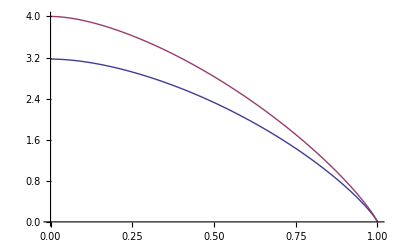

```mathematica
Plot[{(8 (-1+p) Log[(1-p)/9]+(1+8 p) Log[9/(1+8 p)])/Log[512],(64 Log[2]+15 (-1+p) Log[1-p]-(1+15 p) Log[1+15 p])/(16 Log[2])},{p,0,1}]
```

```mathematica
FullSimplify[QuantumEntropy[FullSimplify[1/3 Reshuffle[ChannelMatrixForm[HolevoWernerChannel[2,p,#]&,2]]]],{1>p>0}]
```

(ⅈ (-1+p) π+2 √(1+p (-2+5 p)) ArcCoth[(-1+p)/(√(1+p (-2+5 p)))]+Log[81/p^2])/Log[64]

```mathematica
FullSimplify[QuantumEntropy[FullSimplify[1/4 Reshuffle[ChannelMatrixForm[HolevoWernerChannel[3,p,#]&,3]]]],{1>p>0}]
```

(ⅈ (-1+2 p) π+2 √(1+p (-2+5 p)) ArcCoth[(-1+p)/(√(1+p (-2+5 p)))]+Log[512]-2 Log[p])/Log[256]